```mathematica
color1[a_]:=RGBColor[0,0.6,0];
color2[a_]:=RGBColor[0.3,0,0.3];
```

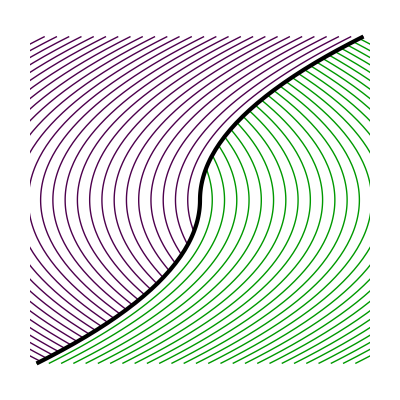

```mathematica
Show[Join[Table[ParametricPlot[{a- y^2/2,-y},{y,-Sqrt[a],2},PlotRange->{{-2,2},{-2,2}},Axes->None,PlotStyle->color1[a]],{a,0,4,0.15}],Table[ParametricPlot[{-a+ y^2/2,y},{y,-Sqrt[a],2},PlotStyle->color2[a],PlotRange->{{-2,2},{-2,2}}],{a,0,4,0.15}],{ParametricPlot[{-y Abs[y]/2,-y},{y,-2,2},PlotStyle->{Black,AbsoluteThickness[3]}]}]]
```

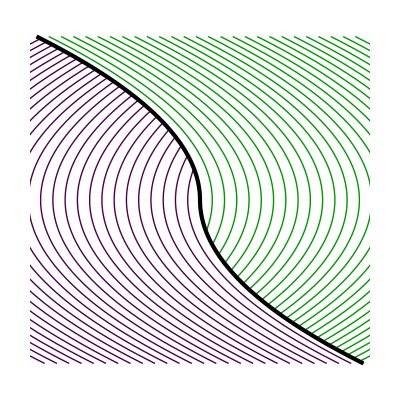

```mathematica
Show[Join[Table[ParametricPlot[{a- y^2/2,y},{y,-Sqrt[a],2},PlotRange->{{-2,2},{-2,2}},Axes->None,PlotStyle->color1[a]],{a,0,4,0.15}],Table[ParametricPlot[{-a+ y^2/2,-y},{y,-Sqrt[a],2},PlotStyle->color2[a],PlotRange->{{-2,2},{-2,2}}],{a,0,4,0.15}],{ParametricPlot[{-y Abs[y]/2,y},{y,-2,2},PlotStyle->{Black,AbsoluteThickness[3]}]}]]
```